```mathematica
DA={52,49,59,29,39,11,41};
DB={32,20,7,12,30,17,10,32,29,39,11,41};
DC={3,29,20,7,12,30,17,10,32,29,39,11,9,32};
```

```mathematica
lik[DD_,κ_,λ_]:=(DD^(-1+κ) ⅇ^(-DD λ) (1/λ)^-κ)/Gamma[κ];
```

```mathematica
prior1[θ_,a_,b_]:=1/(-a+b);
prior2[θ_]:=ⅇ^(-θ/4)/4;
prior3[θ_]:=1/4 ⅇ^(-θ/2) θ;
```

```mathematica
loglik[DD_,κ_,λ_]:=Log[∏_(i=1)^Length[DD] lik[DD[[i]],κ,λ]]//PowerExpand//FullSimplify;
```

```mathematica
loglik[DA,κ,λ]//N
```

25.0629 (-1.+κ)-280. λ+7. κ Log[λ]-7. Log[Gamma[κ]]

```mathematica
(*Integrate out lambda first*)
intLambda1[DD_,a_,κ_]:=∫_a^1 Exp[loglik[DD,κ,λ]]prior1[λ,a,1]prior1[κ,0,25]ⅆλ;
intLambda2[DD_,a_,κ_]:=∫_a^1 Exp[loglik[DD,κ,λ]]prior1[λ,a,1]prior2[κ]ⅆλ;
intLambda3[DD_,a_,κ_]:=∫_a^1 Exp[loglik[DD,κ,λ]]prior1[λ,a,1]prior3[κ]ⅆλ;
```

```mathematica
a=1*10^(-3);
```

```mathematica
ZA1=NIntegrate[intLambda1[DA,a,κ],{κ,0,25}];
Print[ZA1];
Print[Log[ZA1]];
```

1.70133×10^-15

-34.0074

```mathematica
ZB1=NIntegrate[intLambda1[DB,a,κ],{κ,0,25}];
Print[ZB1];
Print[Log[ZB1]];
```

9.30607×10^-23

-50.7288

```mathematica
ZC1=NIntegrate[intLambda1[DC,a,κ],{κ,0,25}];
Print[ZC1];
Print[Log[ZC1]];
```

3.6892×10^-26

-58.5618

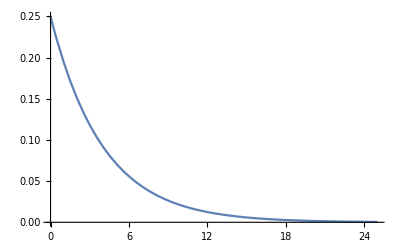

```mathematica
Plot[prior2[κ],{κ,0,25},PlotRange->All]
```

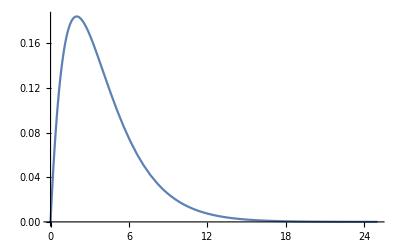

```mathematica
Plot[prior3[κ],{κ,0,25},PlotRange->All]
```

```mathematica
(*Stick with 25 for upper bound on kappa??*)
```

```mathematica
ZA2=NIntegrate[intLambda2[DA,a,κ],{κ,0,Infinity}];
Print[ZA2];
Print[Log[ZA2]];
```

2.47634×10^-15

-33.632

```mathematica
ZB2=NIntegrate[intLambda2[DB,a,κ],{κ,0,Infinity}];
Print[ZB2];
Print[Log[ZB2]];
```

2.07331×10^-22

-49.9277

```mathematica
ZC2=NIntegrate[intLambda2[DC,a,κ],{κ,0,Infinity}];
Print[ZC2];
Print[Log[ZC2]];
```

1.11529×10^-25

-57.4555

```mathematica
ZA3=NIntegrate[intLambda3[DA,a,κ],{κ,0,Infinity}];
Print[ZA3];
Print[Log[ZA3]];
```

3.24986×10^-15

-33.3602

```mathematica
ZB3=NIntegrate[intLambda3[DB,a,κ],{κ,0,Infinity}];
Print[ZB3];
Print[Log[ZB3]];
```

2.87401×10^-22

-49.6012

```mathematica
ZC3=NIntegrate[intLambda3[DC,a,κ],{κ,0,Infinity}];
Print[ZC3];
Print[Log[ZC3]];
```

1.47905×10^-25

-57.1732